# Elliptic Constraints

The plan is to build ellipsoidal constraints out of fully nonlinear constraints
	g_i(x)≥0	
The first thing to do is to build ellipsoidal constraints for a few linear constraints
	c_i+d_i.x≥0. 
The assumption is that we have an interior feasible point
	c_i+d_i.z>0 
and want to build an ellipsoidal constraint
	(x-z).B.(x-z)<Δ
entirely within the feasible set.

Old Pics

## 2 Constraints in 2D

Assuming the center point is at the origin.

{0.644721,0.756853}

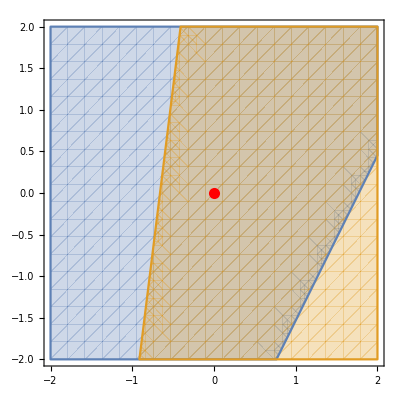

```mathematica
{c1,c2}=RandomReal[{0,1.8},2]
{d1,d2}=RandomReal[{-1,1},{2,2}];
RegionPlot[ {c1+d1.{x,y}>0, c1+d2.{x,y}>0}, {x,-2,2},{y,-2,2},
Epilog->{
{Red,PointSize[0.02],Point[{0,0}]}
}]
```

## 2D with pics

{{-0.248046,2.51069}}

1.22652

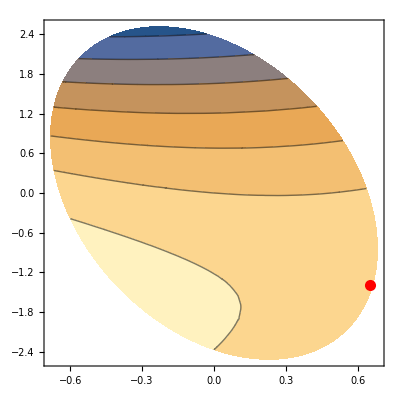

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
g=RandomReal[{-1,1},m];
Δ=0.7;
Ω=ImplicitRegion[{x,y}.B.{x,y}≤Δ^2,{x,y}];
{pStarBI}=NArgMin[{0.5*p.A.p+g.p,p.B.p≤Δ^2},p]
pCP=LinearSolve[A,-g];
M0=ArrayFlatten[({{{{Δ^2}}, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}})];
M1=ArrayFlatten[({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})];
M0Twiddle=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1Twiddle=ArrayFlatten[({{0, B}, {B, 0}})];
Max[Eigenvalues[{M0Twiddle,M1Twiddle}]]
ContourPlot[0.5*{x,y}.A.{x,y}+g.{x,y},{x,y}∈Ω,
Epilog->{{Red,PointSize[0.02],Point[pCP]}}]
```

## Constraints in 3D

Assuming the center point is at a point p. Compute the nearest points on the planes using calc stuff. I have normalized the descriptions of the plane to keep the formulas simple.

```mathematica
{b1,b2}={0.2,0.7};
{n1,n2}=Map[Normalize,{{1.0,0,-3},{1.6,2.4,1}}];
R=2;
p={0.2,0.3,0.4};
{t1,t2}=-{b1,b2};
Show[
ContourPlot3D[ {b1+n1.({x,y,z}-p)==0,b2+n2.({x,y,z}-p)==0},
{x,-R,R},{y,-R,R},{z,-R,R},
ContourStyle->{Directive[Yellow,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}],
ParametricPlot3D[{p+t*n1,p+t*n2},{t, -R,R},PlotStyle->{Yellow, Blue}],
Graphics3D[{PointSize[0.02],
{Red,Point[p]},
{Yellow, Point[ p+t1*n1]},
{Blue, Point[p+t2*n2]}
}],
PlotLabel->{t1,t2}
]
```

-Graphics3D-

The nearest constraint is the yellow one! It is 0.2 from the yellow constraint.  The second nearest constraint is the blue one.  It is 0.5 from the blue constraint. I already sorted them so the nearest constraint is yellow.  Build spheres for each constraint.

```mathematica
Show[
ContourPlot3D[ {b1+n1.({x,y,z}-p)==0,b2+n2.({x,y,z}-p)==0,
Norm[{x,y,z}-p]==-t1,
Norm[{x,y,z}-p]==-t2
},
{x,-R,R},{y,-R,R},{z,-R,R},
ContourStyle->{Directive[Yellow,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}],
ParametricPlot3D[{p+t*n1,p+t*n2},{t, -3,3},PlotStyle->{Yellow, Blue}],
Graphics3D[{PointSize[0.02],
{Red,Point[p]},
{Yellow, Point[ p+t1*n1]},
{Blue, Point[p+t2*n2]}
}],
PlotLabel->{t1,t2}
]
```

-Graphics3D-

What we want to do is to make an ellipsoid (defined by a B matrix just like the GEV-TRS paper) that respects both constraints and a trust region radius of say rMax. First thing is to understand how to represent a matrix for an ellipse.

```mathematica
Show[
ContourPlot3D[ {b1+n1.({x,y,z}-p)==0,b2+n2.({x,y,z}-p)==0,
1/t1^2({x,y,z}-p).({x,y,z}-p)==1,
1/t2^2({x,y,z}-p).({x,y,z}-p)==1},
{x,-R,R},{y,-R,R},{z,-R,R},
ContourStyle->{Directive[Yellow,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}],
ParametricPlot3D[{p+t*n1,p+t*n2},{t, -3,3},PlotStyle->{Yellow, Blue}],
Graphics3D[{PointSize[0.02],
{Red,Point[p]},
(*{Red, Ellipsoid[p,B]},*)
{Yellow, Point[ p+t1*n1]},
{Blue, Point[p+t2*n2]}
}],
PlotLabel->{t1,t2}
]
```

-Graphics3D-

To make an ellipsoid that respects both constraints and a trust region radius rMax.  We keep the nearest constraint direction (assuming we have ordered the constraints appropriately this is n_1) and modify the second direction to be perpendicular to the first direction.   We are going to call the new orthogonal directions q_1 and q_2.

```mathematica
rMax=0.9;
q1=n1;
q2=Normalize[n2-(n2.q1) q1];
B=rMax^2*IdentityMatrix[3]+(t1^2-rMax^2)KroneckerProduct[q1,q1]+(t2^2-rMax^2)KroneckerProduct[q2,q2];
Show[
ContourPlot3D[ {b1+n1.({x,y,z}-p)==0,b2+n2.({x,y,z}-p)==0},
{x,-R,R},{y,-R,R},{z,-R,R},
ContourStyle->{Directive[Yellow,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}],
ParametricPlot3D[{p+t*n1,p+t*n2},{t, -3,3},PlotStyle->{Yellow, Blue}],
Graphics3D[{PointSize[0.02],
{Red,Point[p]},
(*{Red, Ellipsoid[p,B]},*)
{Yellow, Point[ p+t1*n1]},
{Blue, Point[p+t2*n2]},
{Directive[Pink,Opacity[0.5]],Ellipsoid[p,B]}
}],
PlotLabel->√Eigenvalues[B]
]
```

-Graphics3D-

```mathematica
Inverse[B]
```

{{3.87865,0.369015,-7.04045},{0.369015,1.74355,0.123005},{-7.04045,0.123005,22.6532}}

```mathematica
InvB=1/rMax^2*IdentityMatrix[3]+(1/t1^2-1/rMax^2)KroneckerProduct[q1,q1]+(1/t2^2-1/rMax^2)KroneckerProduct[q2,q2]
```

{{3.87865,0.369015,-7.04045},{0.369015,1.74355,0.123005},{-7.04045,0.123005,22.6532}}

Code

## Build B Automatically

The input is a list of values 
	{
	{g_1,∇g_1},
	…
	{g_c,∇g_c}
	}
and a trust region radius Δ.  The output should be a list of orthogonal directions q_1…,q_a and a list of scalars α_1,…,α_a which define B as 
	B=1/Δ(I_m-∑_(i=1)^a q_i⊗q_i)+∑_(i=1)^a α_a q_i⊗q_i=1/Δ I + ∑_(i=1)^a (α_a-1/Δ)q_i⊗q_i
with the condition that the elliptical constraint region
	Ω_e={p∈ℝ^m: p.B.p≤1}
is contained in the original feasible region
	Ω={p∈ℝ^m: g_i+∇g_i.p≥0 for 1≤i≤c}.

The plan is to sort the constraints by distance to the boundary and construct B by projecting out the directions as shown above.

First make sure we can choose only the relevant “near” constraints.

```mathematica
m=2;
c=12;
Δ=0.8;
{gMin,gMax}={0.001,4};
gAndDg=Table[{RandomReal[{gMin,gMax}], RandomReal[{-1,1},m]},c];
NeargDg=Select[ gAndDg, (#⟦1⟧/Norm[#⟦2⟧] <Δ &)]
```

{{0.117484,{0.636913,0.937095}},{0.140902,{0.744653,-0.743449}},{0.0458158,{-0.418973,0.732259}},{0.43927,{0.828069,-0.512878}}}

```mathematica
LinInEqs =Apply[And,Table[ {g, Dg}=gAndDg⟦i⟧;
g+Dg.{p1,p2}≥0,{i, Length[gAndDg]}]];
NearLinInEqs =Apply[And,Table[ {g, Dg}=NeargDg⟦i⟧;
g+Dg.{p1,p2}≥0,{i, Length[NeargDg]}]];
TabView[{"All"->RegionPlot[LinInEqs,
{p1,-3,3},{p2,-3,3},PlotPoints->20,
Prolog->{EdgeForm[Red],LightPink,Disk[{0,0},Δ]}],
"Near"->RegionPlot[NearLinInEqs,
{p1,-3,3},{p2,-3,3},PlotPoints->20,
Prolog->{EdgeForm[Red],LightPink,Disk[{0,0},Δ]}]}
]
```

12

The next step is to sort the inequalities by distance and extract the directions.  I am going to use a QR decomposition to build the orthogonal directions

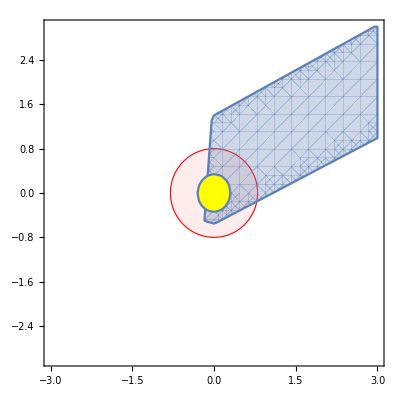

```mathematica
m=2;
c=12;
Δ=0.8;
{gMin,gMax}={0.001,4};
gAndDg=Table[{RandomReal[{gMin,gMax}], RandomReal[{-1,1},m]},c];
LinInEqs =Apply[And,Table[ {g, Dg}=gAndDg⟦i⟧;
g+Dg.{p1,p2}≥0,{i, Length[gAndDg]}]];
NeargDg=Select[ gAndDg, Abs[#⟦1⟧]/Norm[#⟦2⟧] <Δ &];
(* Sort by distance and make sure there are not more than m directions *)
NeargDg=Sort[NeargDg, Abs[#1⟦1⟧]/Norm[#1⟦2⟧]<Abs[#2⟦1⟧]/Norm[#2⟦2⟧]&]⟦1;;UpTo[m]⟧;
(* Construct Orthogonal Directions using QR decomposition *)
NearConsCount=Length[NeargDg];
B=1/Δ IdentityMatrix[m];
If[NearConsCount!=0,
Qs=QRDecomposition[NeargDg⟦All,2⟧ᵀ]⟦1⟧;
(* Construct Lengths *)
αs=Table[ NeargDg⟦i,1⟧/Norm[NeargDg⟦i,2⟧] Abs[Qs⟦i⟧.NeargDg⟦i,2⟧],{i,NearConsCount}];
Do[ 
B += 1/Δ(1/αs⟦i⟧-1)KroneckerProduct[Qs⟦i⟧,Qs⟦i⟧],
{i,NearConsCount}]
]
Show[
RegionPlot[LinInEqs,
{p1,-3,3},{p2,-3,3},PlotPoints->20,
Prolog->{EdgeForm[Red],
{LightPink,Disk[{0,0},Δ]}
}],
RegionPlot[ {p1,p2}.B.{p1,p2}≤1,{p1,-3,3},{p2,-3,3},
PlotStyle->Yellow,PlotPoints->20]
]
```

```mathematica
QRDecomposition[NeargDg⟦All,2⟧ᵀ]⟦1⟧
```

{{-0.0135285,0.999908}}

```mathematica
Q=QRDecomposition[NeargDg⟦All,2⟧]⟦1⟧;
(* Construct Lengths *)
Distances=Table[NeargDg⟦i,1⟧/Abs[NeargDg⟦i,2⟧.Q⟦i⟧],{i,Length[NeargDg]}]
```

{{0,0},{0,0}}

{1.90571,0.140245}

```mathematica
?Sort
```

```mathematica
Range[4]⟦1;;UpTo[5]⟧
```

{1,2,3,4}

```mathematica
?UpTo
```

```mathematica
If[ Length[NeargDg]==0, B= 1/Δ IdentityMatrix[m],
(* Sort by Nearness *)
NeargDg=Sort[NeargDg, Abs[#1⟦1⟧]/Norm[#1⟦2⟧]<Abs[#2⟦1⟧]/Norm[#2⟦2⟧]&];
(* Construct Orthogonal Directions *)
Q=QRDecomposition[A]⟦1⟧;
Map[Dimensions,{Q,gDg⟦All,2⟧}]
(* Construct Lengths *)
αs=Table[gDg⟦i,1⟧/(gDg⟦i,2⟧.Q⟦i⟧),{i, Length[gDg]}];
B=1/Δ IdentityMatrix[m]+Sum[(1/αs⟦i⟧-1/Δ)KroneckerProduct[Q⟦i⟧,Q⟦i⟧],{i,Length[gDg]}]
]
```

```mathematica
LinInEqs =Apply[And,Table[ {g, Dg}=gDg⟦i⟧;
g+Dg.{p1,p2}≥0,{i, Length[gDg]}]];
NearLinInEqs =Apply[And,Table[ {g, Dg}=NeargDg⟦i⟧;
g+Dg.{p1,p2}≥0,{i, Length[NeargDg]}]];

TabView[{"All"->RegionPlot[LinInEqs,
{p1,-3,3},{p2,-3,3},PlotPoints->20,
Prolog->{EdgeForm[Red],LightPink,Disk[{0,0},Δ]}],
"Near"->RegionPlot[NearLinInEqs,
{p1,-3,3},{p2,-3,3},PlotPoints->20,
Prolog->{EdgeForm[Red],LightPink,Disk[{0,0},Δ]}]}
]
```

Dot::dotsh: Tensors {-0.552694,-0.766324} and {-0.49429,0.175708,-0.449494,0.284818,-0.498433,0.176771,-0.402436} have incompatible shapes.

Dot::dotsh: Tensors {-0.759381,-0.729478} and {0.24173,-0.167722,-0.0309078,-0.660251,-0.127669,-0.0686671,-0.674933} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Part::partw: Part 3 of {{-0.49429,0.175708,-0.449494,0.284818,-0.498433,0.176771,-0.402436},{0.24173,«5»,-0.674933}} does not exist.

Part::partw: Part 4 of {{-0.49429,0.175708,-0.449494,0.284818,-0.498433,0.176771,-0.402436},{0.24173,«5»,-0.674933}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{2,7},{12,2}} {0.155491/({-0.552694,-0.766324}.{-0.49429,«5»,-0.402436}),0.535085/({-0.759381,-«19»}.{«1»}),(«19»)/(«1»),«5»,«1»,(«19»)/({«1»}.«1»),«2»} cannot be combined.

Thread::tdlen: Objects of unequal length in {{0.526316,0.},{0.,0.526316}}+{{0.0584332 (-0.526316+1.86886 Dot[«2»])+«9»+«2»,«5»,-0.163151 (-0.526316+«19» Dot[«2»])+«9»+«2»},«6»} cannot be combined.

{{0.526316,0.},{0.,0.526316}}+{{1},{12+1,5,1},3,{1,1,3,1,1},{1}}
 |  |  |  |

12

More visual testing

```mathematica
m=3;
c=12;
Δ=0.2;
{gMin,gMax}={0.001,4};
gDg=Table[{RandomReal[{gMin,gMax}], RandomReal[{-1,1},m]},c];
LinInEqs =Apply[And,Table[ {g, Dg}=gDg⟦i⟧;
g+Dg.{p1,p2,p3}≥0,{i, Length[gDg]}]];
RegionPlot3D[
LinInEqs,
{p1,-3,3},{p2,-3,3},{p3,-3,3},
PlotPoints->100]
```

-Graphics3D-

Automatic testing using RegionWitin

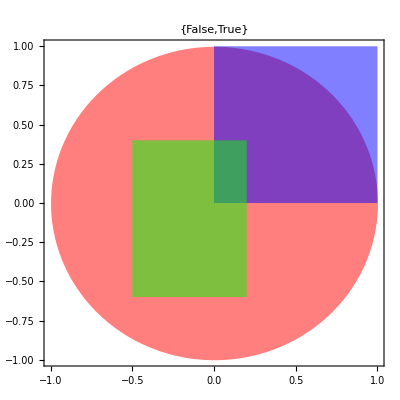

```mathematica
Ω1=Disk[];
Ω2=Rectangle[];
Ω3=Rectangle[{-0.5,-0.6},{0.2,0.4}];
Graphics[{
Opacity[0.5],
{Red,Ω1},
{Blue,Ω2},
{Green,Ω3}
},Frame->True,
PlotLabel->{RegionWithin[Ω1,Ω2],RegionWithin[Ω1,Ω3]}]
```